```mathematica
Clear["Global`*"]
```

Primeira parte: matrizes aleatórias com elementos escolhidos a partir da distribuição normal

```mathematica
Ntot=2;
M = 10000;
difer = {};
For [j = 1,j≤M,j+=1,
(mat= RandomVariate[NormalDistribution[],{Ntot,Ntot}])//MatrixForm;
lambda=Sort[Eigenvalues[(mat+Transpose[mat])/2]];
dlambda=lambda[[Ntot/2+1]]-lambda[[Ntot/2]];
AppendTo[difer,dlambda]
]
difernorm=difer/Mean[difer];
```

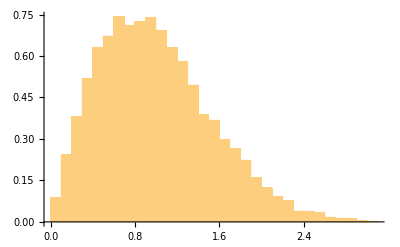

```mathematica
P2=Histogram[difernorm,{1/10},"PDF"]
```

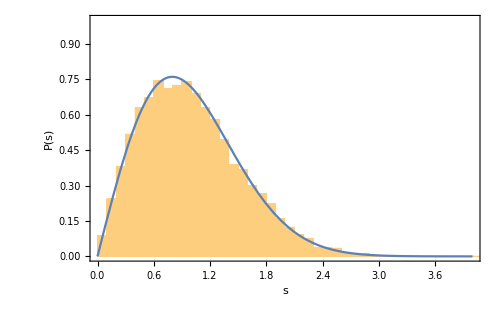

```mathematica
Grafico=Show[P2,Pa,AxesOrigin->{0.0,0.0},Frame->True,FrameLabel->{"s","P(s)"},PlotRange->{{0,4.0},{0,1.0}},PlotRangePadding->None,LabelStyle->{FontFamily-> "CMU Serif",FontSize->30},ImageSize->500]
```

Segunda parte: matrizes simétricas formadas com elementos escolhidos de uma distribuição binária de -1 e +1

```mathematica
Ntot=2;
M = 10000;
difer = {};
For [j = 1,j≤M,j+=1,
(temp= RandomInteger[{0,1},{Ntot,Ntot}])//MatrixForm;
mat = ConstantArray[1,{Ntot,Ntot}]-2*temp;
matsim = UpperTriangularize[mat]+Transpose[UpperTriangularize[mat,1]]; 
lambda=Sort[Eigenvalues[N[matsim]]];
dlambda=lambda[[Ntot/2+1]]-lambda[[Ntot/2]];
AppendTo[difer,dlambda]
]
difernorm=difer/Mean[difer];
```

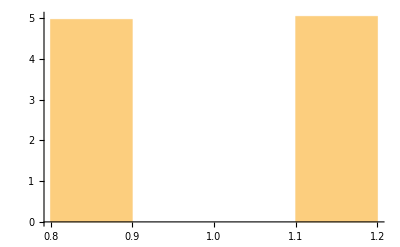

```mathematica
P2b=Histogram[difernorm,{1/10},"PDF"]
```